```mathematica
n=12;
m=4;
alpha=0.5;
prefix="N="<>ToString[n]<>"_M="<>ToString[m]<>"_alpha="<>ToString[alpha];
SetDirectory["/home/leonard/Documents/Projects/PhysicalDistance/Codes/data/spinChain/"<>prefix];
dosData=Import["./DoSdata.txt","Table"];
corr=Import["./emd_kl.txt","Table"];
eigD=Flatten[Import["./DMat.txt","Table"]];
esp=Import["./EspacingData.txt","Table"];
ind=Import["./ind.dat","Table"]//Flatten;
pos=Import["./pos.dat","Table"]//Flatten;
```

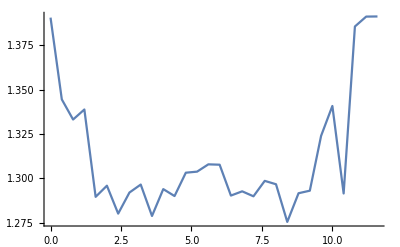

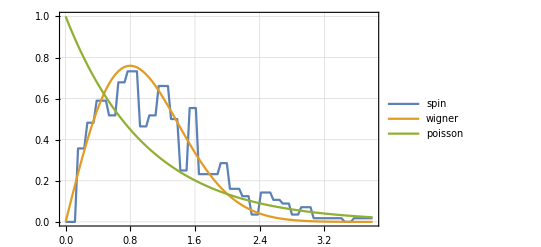

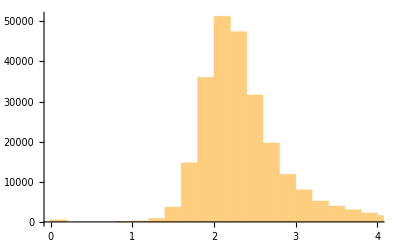

```mathematica
(*ListLinePlot[dosData]*)
ListLinePlot[Transpose[{pos,ind}]]
xs=esp⟦;;,1⟧;
ys=esp⟦;;,2⟧;
wig=esp⟦;;,3⟧;
poi=esp⟦;;,4⟧;
ListLinePlot[{Transpose[{xs,ys}],Transpose[{xs,wig}],Transpose[{xs,poi}]},{PlotTheme->"Detailed",PlotRange->All,PlotLegends->{"spin","wigner","poisson"}}]
Histogram[eigD]
```

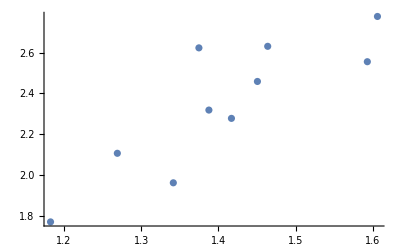

```mathematica
ListPlot[corr]
```

```mathematica
alphaLis={0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.5,0.6,0.7};
resGross=ParallelTable[
n=12;
m=4;
prefix="N="<>ToString[n]<>"_M="<>ToString[m]<>"_alpha="<>ToString[alpha];
SetDirectory["/home/leonard/Documents/Projects/PhysicalDistance/Codes/data/spinChain/"<>prefix];
(*dosData=Import["./DoSdata.txt","Table"];
corr=Import["./emd_kl.txt","Table"];

ind=Import["./ind.dat","Table"]//Flatten;
pos=Import["./pos.dat","Table"]//Flatten;*)
esp=Import["./EspacingData.txt","Table"];
eigD=Flatten[Import["./DMat.txt","Table"]];{eigD,esp},{alpha,alphaLis}
];
```

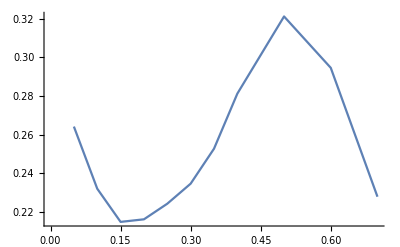

```mathematica
res1=resGross[[;;,1]];
ListLinePlot[{{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.5,0.6,0.7},Variance[#]&/@res1}//Transpose]
```

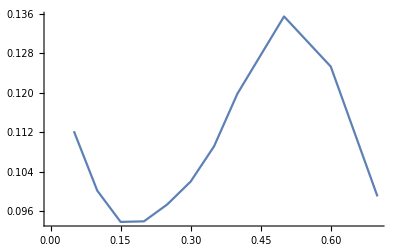

```mathematica
res1=resGross[[;;,1]];
ListLinePlot[{{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.5,0.6,0.7},Variance[#]/Mean[#]&/@res1}//Transpose]
```

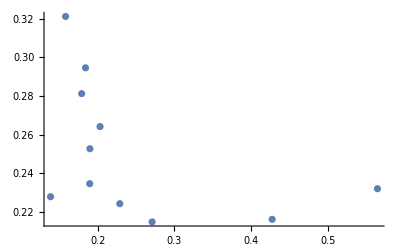

```mathematica
res2=resGross[[;;,2]];
distD={Norm[#[[2]]-#[[3]]],Norm[#[[2]]-#[[4]]]}&/@res2;
ListPlot[{distD[[;;,2]],Variance[#]&/@res1}//Transpose]
```